# Generation Routines for Spatial Layouts

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
<<PajaroLocoPublic`
nonMigratoryForce=1000;
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
CalculateMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
ListPlotPoints[points_]:=ListPlot[points,
Frame->True,
Axes->True,
FrameStyle->Thickness[.005],
ImageSize->800,
FrameTicksStyle->None,
PlotStyle->PointSize[.025],
AspectRatio->1
]Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Black,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
Themes`AddThemeRules["RandomPointsPlot",
AspectRatio->1,
Frame->True,
FrameLabel->(Style[#,20]&/@{"x (meters)","y (meters)"}),
FrameTicksStyle->20,
FrameStyle->Thick,
FrameTicks->{{None,All},{None,All}},
PlotStyle->Directive[PointSize[.02],Opacity[.75]],
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
Themes`AddThemeRules["RandomPointsMatrix",
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicks->{{None,None},{None,None}},
ColorFunction->"LakeColors",
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
DistributionIntoKernel[distribution_,center_,n_]:=Table[center+{Re[#],Im[#]}&[RandomReal[distribution] ⅇ^(ⅈ RandomReal[{0,2π}])],{n}]
MapDistributionParametersOnPoints[distribution_,centers_,n_]:=Join@@(DistributionIntoKernel[distribution,#,n]&/@centers)
SphereDistance[{ϕ1_,θ1_},{ϕ2_,θ2_},r_]:=r InverseHaversine[Haversine[ϕ1-ϕ2]+Cos[ϕ1]Cos[ϕ2]Haversine[θ1-θ2]]
SphereDistanceBetweenPoints[sphericalCoordinates1_,sphericalCoordinates2_]:=Module[{tuple},
tuple={
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates1],
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates2]
};
SphereDistance[{tuple[[1,2]],tuple[[1,3]]},{tuple[[2,2]],tuple[[2,3]]},tuple[[1,1]]]
]
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameTicks->{None,None},
Filling->Bottom,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
BaseStyle->15,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Opacity[.5]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
```

/Users/sanchez.hmsc/Documents/GitHub/MGDrivE/BRInE

RandomPointsPlot

RandomPointsMatrix

```mathematica
customPlot[data_,o___]:=Block[{xmin,xmax,ymin,ymax,x,y,mainplot,xhist,yhist,opts=Flatten[{o}]},{x,y}=Transpose[data];
xhist=HistogramList[x,50];
yhist=HistogramList[y,50];
{xmin,xmax}=Through[{Min,Max}[First[xhist]]];
{ymin,ymax}=Through[{Min,Max}[First[yhist]]];
mainplot=ListPlot[data,Frame->{{True,True},{True,True}},Axes->False,FrameTicks->None,AspectRatio->1,PlotRange->{{xmin,xmax},{ymin,ymax}},PlotRangePadding->Scaled[0.02],ImagePadding->{{None,1},{None,1}},FilterRules[opts,Options[ListPlot]],FrameStyle->GrayLevel[0.3],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];
xhist=Histogram[x,{First[xhist]},Frame->{{True,True},{True,False}},FrameTicks->{{None,None},{Automatic,None}},Axes->False,AspectRatio->1/3,ImagePadding->{{1,1},{None,All}},FilterRules[opts,Options[Histogram]],GridLines->{Automatic,None},FrameStyle->GrayLevel[0.3],GridLinesStyle->Directive[Gray,Dotted]];
yhist=Histogram[y,{First[yhist]},Frame->{{True,False},{True,True}},Axes->False,FrameTicks->{{Automatic,None},{None,None}},AspectRatio->3,BarOrigin->Left,ImagePadding->{{All,None},{1,1}},FilterRules[opts,Options[Histogram]],GridLines->{None,Automatic},FrameStyle->GrayLevel[0.3],GridLinesStyle->Directive[Gray,Dotted]];
Graphics[{{Opacity[0],Point[{{360,360},{-120,-120}}]},Inset[mainplot,{0,0},{Left,Bottom},{360,360}],Inset[xhist,{0,0},{Left,Top},{360,Automatic}],Inset[yhist,{0,0},{Right,Bottom},{Automatic,360}]},PlotRange->{{-120,360},{-120,360}},FilterRules[opts,Options[Graphics]],ImagePadding->{{30,1},{30,1}}]]
customPlot[sampledCoordinates];
```

Set::shape: Lists {x,y} and Transpose[sampledCoordinates] are not the same shape.

HistogramList::ldata: x is not a valid dataset or list of datasets.

HistogramList::ldata: y is not a valid dataset or list of datasets.

General::stop: Further output of HistogramList::ldata will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{x,x},{y,y}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: sampledCoordinates is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{x,x},{y,y}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: sampledCoordinates is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{x,x},{y,y}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot::prng will be suppressed during this calculation.

ListPlot::lpn: sampledCoordinates is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Histogram::hbins: The bin specification {x} cannot be used to determine either how many or which bins to use.

General::stop: Further output of Histogram::hbins will be suppressed during this calculation.

## Regular Patterns

## Point Distribution

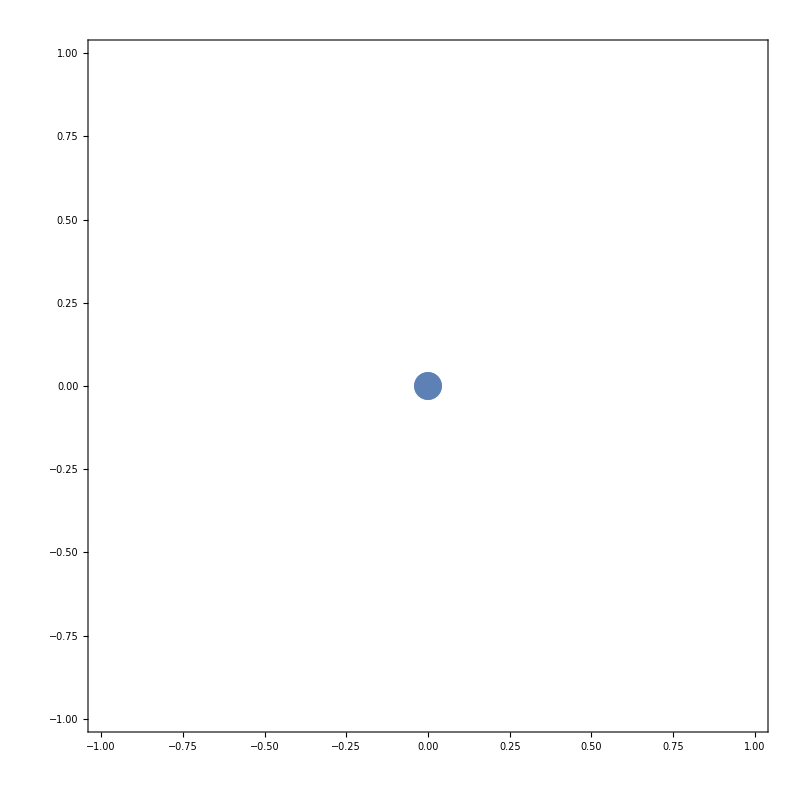

matrixTransitions.csv

matrixCoordinates.csv

```mathematica
points={{0,0}};
distancesMatrix={{1}};
(**)
ListPlotPoints[points]
(**)
migrationProbabilities=CalculateMigrationProbabilities[distancesMatrix,nonMigratoryForce];
(**)
Export["matrixTransitions.csv",migrationProbabilities]
Export["matrixCoordinates.csv",points]
```

## Line Distribution

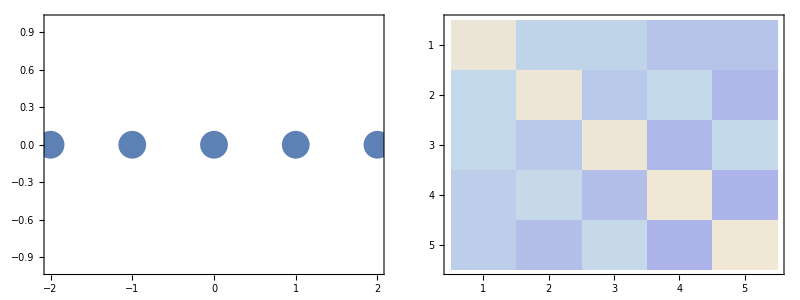

matrixTransitions.csv

matrixCoordinates.csv

```mathematica
{height,stepSize,pointsNumber}={0,1,2};
points=Table[{{-i,height},{i,height}},{i,1,pointsNumber,1}]//Flatten[#,1]&//Prepend[#,{0,0}]&;
distancesMatrix=Table[
EuclideanDistance[points[[i]],#]&/@points
,{i,1,points//Length}];
migrationProbabilities=CalculateMigrationProbabilities[distancesMatrix,nonMigratoryForce]//N;
(**)
listPlot=ListPlotPoints[points];
matrixPlot=migrationProbabilities//MatrixPlot[#,ColorFunction->"LakeColors",ImageSize->800]&;
Grid[{{listPlot,matrixPlot}}]
(**)
Export["matrixTransitions.csv",migrationProbabilities]
Export["matrixCoordinates.csv",points]
```

## Grid Distribution

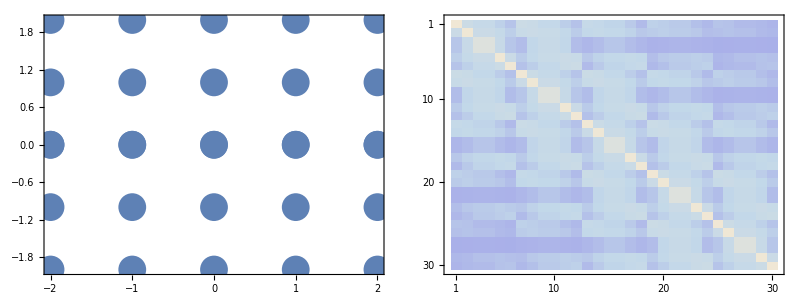

matrixTransitions.csv

matrixCoordinates.csv

```mathematica
{height,stepSize,pointsNumber}={0,1,2};
points=
Table[
{
Table[{{-i,j},{i,j}},{i,1,pointsNumber,stepSize}]//Flatten[#,1]&//Prepend[#,{0,j}]&,
Table[{{-i,-j},{i,-j}},{i,1,pointsNumber,stepSize}]//Flatten[#,1]&//Prepend[#,{0,-j}]&
}//Flatten[#,1]&
,{j,0,pointsNumber}]//Flatten[#,1]&//Sort;
distancesMatrix=Table[EuclideanDistance[points[[i]],#]&/@points,{i,1,points//Length}];
migrationProbabilities=CalculateMigrationProbabilities[distancesMatrix,nonMigratoryForce]//N;
(**)
listPlot=ListPlotPoints[points];
matrixPlot=migrationProbabilities//MatrixPlot[#,ColorFunction->"LakeColors",ImageSize->800]&;
Grid[{{listPlot,matrixPlot}}]
(**)
Export["matrixTransitions.csv",migrationProbabilities]
Export["matrixCoordinates.csv",points]
```

## Cube Distribution

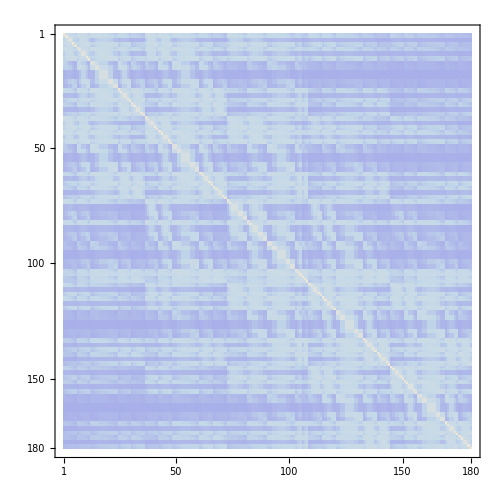
-Graphics3D- | -Graphics-

matrixTransitions.csv

matrixCoordinates.csv

```mathematica
{height,stepSize,pointsNumber}={0,1,2};
points=
Table[
Table[
{
Table[{{-i,-j,-k},{i,-j,-k}},{i,1,pointsNumber,stepSize}]//Flatten[#,1]&//Prepend[#,{0,-j,-k}]&,
Table[{{-i,-j,k},{i,-j,k}},{i,1,pointsNumber,stepSize}]//Flatten[#,1]&//Prepend[#,{0,-j,k}]&,
Table[{{-i,j,-k},{i,j,-k}},{i,1,pointsNumber,stepSize}]//Flatten[#,1]&//Prepend[#,{0,j,-k}]&,
Table[{{-i,j,k},{i,j,k}},{i,1,pointsNumber,stepSize}]//Flatten[#,1]&//Prepend[#,{0,-j,k}]&
}//Flatten[#,1]&
,{j,0,pointsNumber}]
,{k,0,pointsNumber}]//Flatten[#,2]&//Sort;
distancesMatrix=Table[
EuclideanDistance[points[[i]],#]&/@points
,{i,1,points//Length}];
migrationProbabilities=CalculateMigrationProbabilities[distancesMatrix,nonMigratoryForce]//N;
(**)
listPlot=ListPointPlot3D[points,AspectRatio->1,PlotStyle->PointSize[.025],ImageSize->500];
matrixPlot=migrationProbabilities//MatrixPlot[#,ColorFunction->"LakeColors",ImageSize->500]&;
Grid[{{listPlot,matrixPlot}}]
(**)
Export["matrixTransitions.csv",migrationProbabilities]
Export["matrixCoordinates.csv",points]
```

## Random Patterns

## Random Pattern

```mathematica
citiesDummy=Accumulate[RandomReal[{-100,100},{50,2}]];
names=ToString/@Range[citiesDummy//Length];
pops=RandomInteger[1000,citiesDummy//Length];
cities=Transpose[{names,citiesDummy,pops}];
distances=CalculateEuclideanDistances[citiesDummy];
migration=CalculateMigrationProbabilities[distances,1000];
ListPlot[
Table[Callout[citiesDummy[[i]],i],{i,1,Length[citiesDummy]}],
Frame->True,
Axes->False,
AspectRatio->1,
FrameStyle->Thickness[.005],
ImageSize->800,
FrameTicksStyle->None
]
Export["accumulateCityDARPA.csv",Flatten/@cities]
Export["accumulateCityTransitionsDARPA.csv",migration]
```

-Graphics-

accumulateCityDARPA.csv

accumulateCityTransitionsDARPA.csv

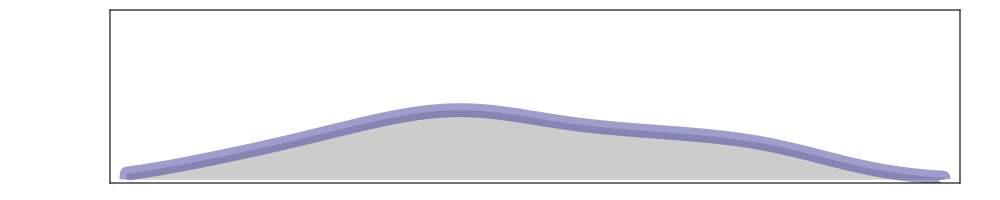
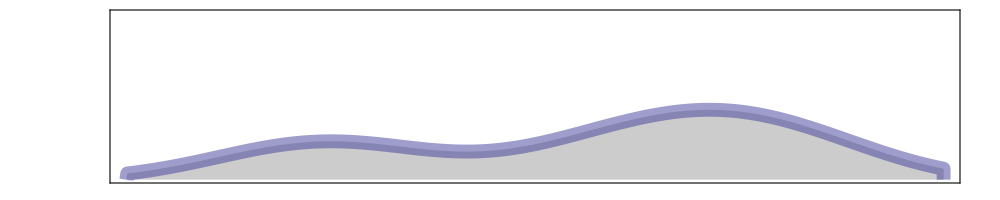
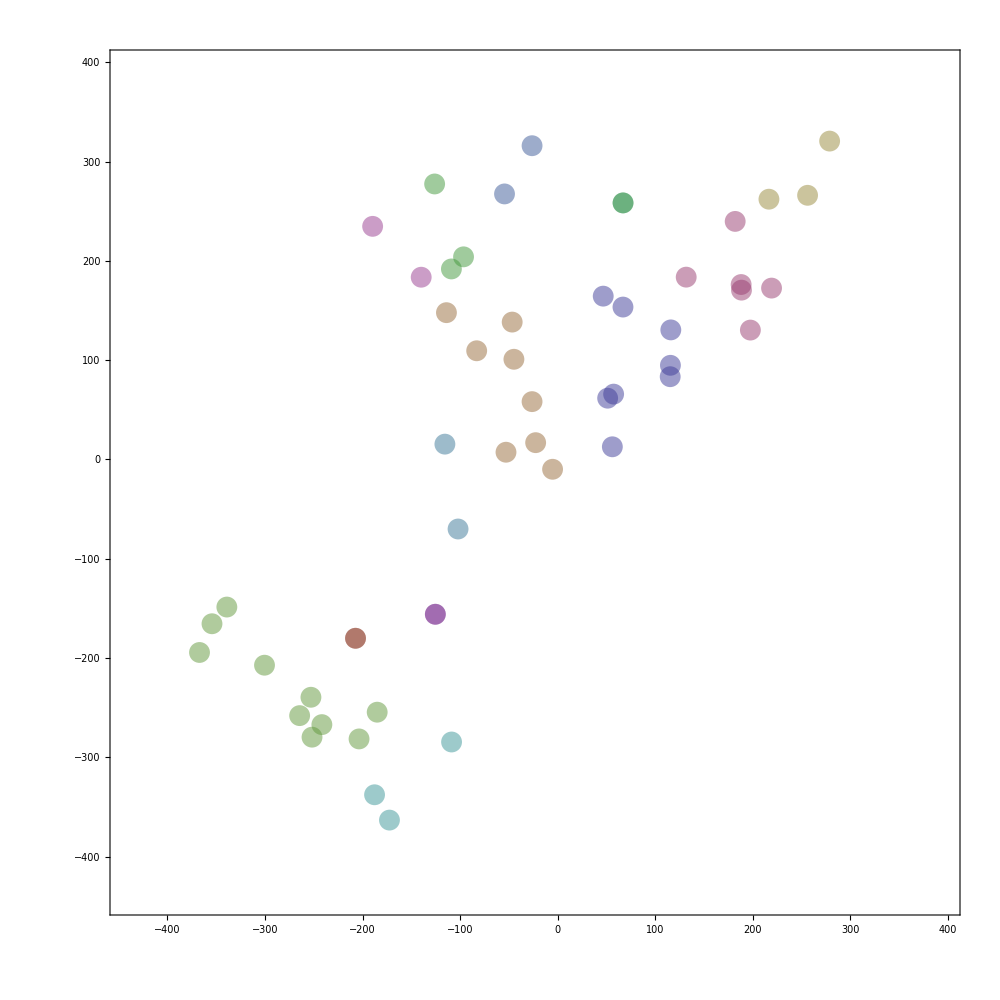
| -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
min=Flatten[citiesDummy]//Min;
max=Flatten[citiesDummy]//Max;
{imageSize,imagePadding,plotRange}={1000,50,{{min-75,max+75},{0,.005}}};
sampledCoordinates=citiesDummy;
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
eucledianDistances=CalculateEuclideanDistances[sampledCoordinates];
(**)
histograms=SmoothHistogramPlot[#,{imageSize,imagePadding},plotRange]&/@Transpose[sampledCoordinates];
scatter=ListPlotScatter[clusteredCoordinates,{imageSize,imagePadding},plotRange];
grid=Grid[{
{"",Rotate[histograms[[1]]//Show[#,ImagePadding->{{imagePadding,imagePadding},{0,0}}]&,0Degree],""},
{Rotate[histograms[[2]]//Show[#,ImagePadding->{{imagePadding,imagePadding},{0,0}}]&,90Degree],scatter//Show[#,ImagePadding->{{imagePadding,imagePadding},{imagePadding,imagePadding}}]&,""}
}];
grid=Grid[{{grid(*,MatrixPlot[eucledianDistances,ColorFunction->"LakeColors",ImageSize->imageSize]*)}}]
```

## Geographical Data

## Country

```mathematica
countryName="Madagascar";
cities=CountryData[countryName,"LargestCities"];
countryMap=CountryData[countryName,"Polygon"];
cityCoordinates=Reverse[CityData[#,"Coordinates"]]&/@cities;
missing=Position[cityCoordinates,Missing["NotAvailable"]];
cityCoordinates=Delete[cityCoordinates,missing]//ToExpression;
distances=CalculateEuclideanDistances[cityCoordinates];
migrationProbabilities=CalculateMigrationProbabilities[distances,nonMigratoryForce];
migrationProbabilities//MatrixForm;
```

```mathematica
graph=GraphTransitionsFrequenciesWithMax[
{
migrationProbabilities//LowerTriangularize//Chop//ReplacePart[#,{i_,i_}->0]&,
ToString/@Range[migrationProbabilities//Length]
},.0025,
VariableStyle->"LineWidth",
VertexCoordinates->cityCoordinates,
Prolog->{EdgeForm[Directive[Thickness[.005],Black]],Lighter[White,.75],countryMap},
ImageSize->800,
VertexLabelStyle->.01,
VertexStyle->Directive[{EdgeForm[Directive[{Thickness[.005],Black}]],Opacity[1],Darker[White,1]}],
VertexSize->1,
Background->White(*Lighter[LightBlue,.9]*),
Frame->False,
ImagePadding->50,
FrameStyle->Thickness[.01]
]
(*Export[countryName<>"Clustered.png",%,ImageResolution->500]*)
```

-Graphics-

## Region

```mathematica
{state,country}={"California","UnitedStates"};
cities=CityData[{Large,state,country}];
countryMap=CountryData[country,"Polygon"];
cityCoordinates=Reverse[CityData[#,"Coordinates"]]&/@cities;
(**)
distances=CalculateEuclideanDistances[cityCoordinates];
migrationProbabilities=CalculateMigrationProbabilities[distances,nonMigratoryForce];
migrationProbabilities//MatrixForm;
```

```mathematica
GraphTransitionsFrequenciesWithMax[
{
migrationProbabilities//LowerTriangularize//Chop//ReplacePart[#,{i_,i_}->0]&,
ToString/@Range[migrationProbabilities//Length]
},.0025,
VariableStyle->"LineWidth",
VertexCoordinates->cityCoordinates,
ImageSize->800,
VertexLabelStyle->.01,
VertexStyle->Directive[{EdgeForm[Directive[{Thickness[.0025],White}]],Opacity[1],Darker[White,1]}],
VertexSize->1.5,
Background->White,
Frame->True,
ImagePadding->0,
FrameStyle->Thickness[.01],
Prolog->{EdgeForm[Directive[Thickness[.0075],Black]],Darker[White,0],countryMap}
]
Export["california.png",%,ImageSize->2000,ImageResolution->500]
```

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::partd: Part specification {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,«22»}⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Graph[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72},VertexNumberToVertexSyllable[1->{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72}⟦2,1⟧,2->1→0.000542565->3->1],16,Background→GrayLevel[1],ImagePadding→0]
 |  |  |  |

Rasterize::bigraster: Not enough memory available to rasterize Notebook expression.

$Failed

## Random Topologies

## Network

```mathematica
distribution=SpatialGraphDistribution[600,0.15];
graph=RandomGraph[distribution]//AdjacencyMatrix;
names=ToString/@(Range[graph[[1]]//Length]);
netPlot=GraphTransitionsFrequenciesWithMax[
{
graph//LowerTriangularize//Chop//ReplacePart[#,{i_,i_}->0]&,
names
},1
];
coords=AbsoluteOptions[netPlot,VertexCoordinates][[1,2]];
distancesMatrix=Table[EuclideanDistance[coords[[i]],#]&/@coords,{i,1,Length[coords]}];
probabilities=ReplaceAll[Quiet[(1/distancesMatrix)],ComplexInfinity->0];
thresheld=Table[If[#>1.5,#,0]&/@i,{i,probabilities}];
netPlot2=GraphTransitionsFrequenciesWithMax[
{
thresheld//LowerTriangularize//Chop//ReplacePart[#,{i_,i_}->0]&,
names
},5,
VariableStyle->"Both",
VertexCoordinates->coords,
ImageSize->2000,
LineThickness->.002,
VertexLabelStyle->.01,
VertexStyle->Directive[{EdgeForm[Directive[{Thickness[.001],White}]],Opacity[1],Darker[White,1]}],
VertexSize->2,
Background->White(*Lighter[LightBlue,.9]*),
Frame->False,
ImagePadding->0,
FrameStyle->Thickness[.01]
];
Export["NetworkBackground.png",netPlot2,ImageSize->7500,ImageResolution->500]
```

NetworkBackground.png

## Points

### Symmetric

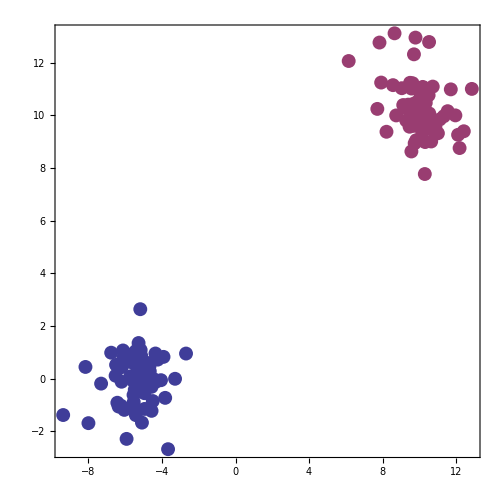
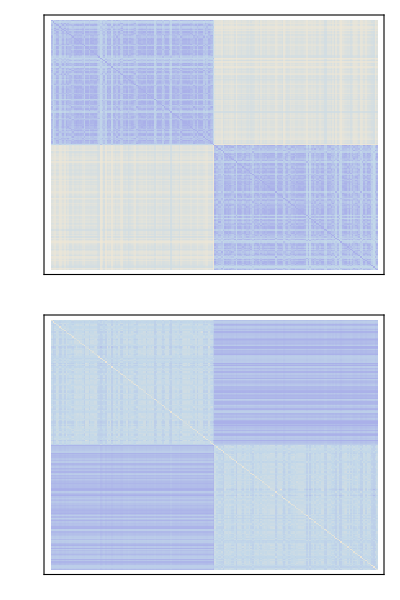
-Graphics- | -Graphics-

```mathematica
{samples,centers}={100,{{-5,0},{10,10}}};
nonMigratoryForce=100;
(*PointsGeneration*)
distribution=LaplaceDistribution[0,1];
points=MapDistributionParametersOnPoints[distribution,centers,samples];
clusters=FindClusters[points];
(*Distances*)
distances=CalculateEuclideanDistances[points];
probabilities=CalculateMigrationProbabilities[distances,nonMigratoryForce];
(*Plots*)
pointsPlot=ListPlot[clusters,PlotTheme->"RandomPointsPlot",ImageSize->500];
distancesPlot=MatrixPlot[distances,PlotTheme->"RandomPointsMatrix",ImageSize->245];
probabilitiesPlot=MatrixPlot[probabilities,PlotTheme->"RandomPointsMatrix",ImageSize->245];
Grid[{{pointsPlot,Grid[{{distancesPlot},{probabilitiesPlot}}]}}]
```

### Sphere

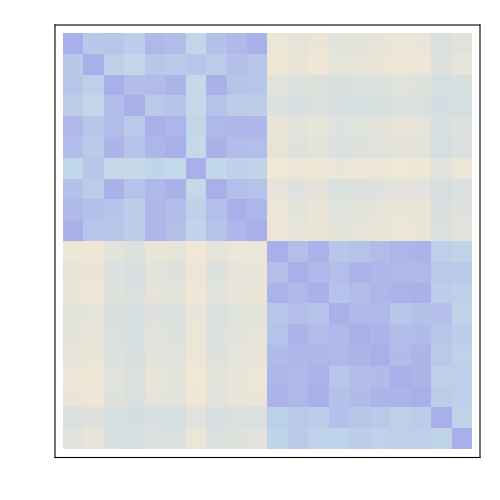
-Graphics3D- | -Graphics-

```mathematica
{samples,centers,radius}={10,{{10,0},{0,-10}},25};
nonMigratoryForce=100;
(*PointsGeneration*)
distribution=NormalDistribution[0,2];
points=MapDistributionParametersOnPoints[distribution,centers,samples];
points3D={#[[1]],#[[2]],Sqrt[radius^2-(#[[1]])^2-(#[[2]])^2]}&/@points;
sphere=Show[{
Graphics3D[{Blue,Opacity[.5],Specularity[Black,10],Sphere[{0,0,0},radius]}],
ListPointPlot3D[points3D,PlotStyle->{PointSize[.0075],Opacity[.5],Black}]
},Boxed->False,ImageSize->750];
distance=Table[SphereDistanceBetweenPoints[points3D[[i]],#]&/@points3D,{i,1,Length[points3D]}];
matrix=MatrixPlot[distance,PlotTheme->"RandomPointsMatrix",ImageSize->500];
Grid[{{sphere,matrix}}]
```

### Asymmetric

#### Basic Test

```mathematica
points=Join[{
DistributionIntoKernel[WeibullDistribution[1,20],{-20,-20},25],
DistributionIntoKernel[NormalDistribution[0,20],{20,20},25]
}];
ListPlot[points,PlotRange->{{-50,50},{-50,50}},PlotTheme->"RandomPointsPlot"];
```

#### Complex Test

```mathematica
points=Join[{
DistributionIntoKernel[WeibullDistribution[2,25],{-25,-25},25],
DistributionIntoKernel[NormalDistribution[0,20],{50,50},25]
}];
sampledCoordinates=Flatten[points,1];
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
eucledianDistances=CalculateEuclideanDistances[sampledCoordinates];
```

```mathematica
(*Cluster Sort Attempt*)
clustersPosition=Position[clusteredCoordinates,#][[1,1]]&/@sampledCoordinates;
CalculateEuclideanDistances[sampledCoordinates[[clustersPosition]]]//MatrixPlot;
```

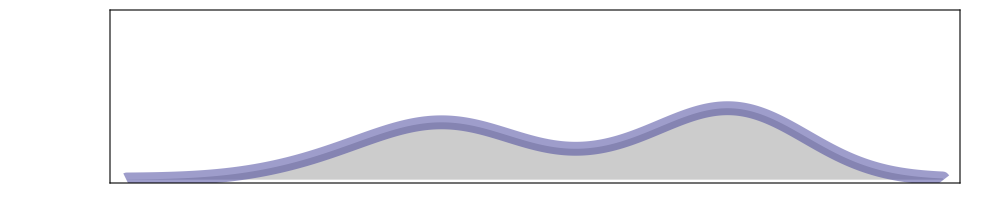
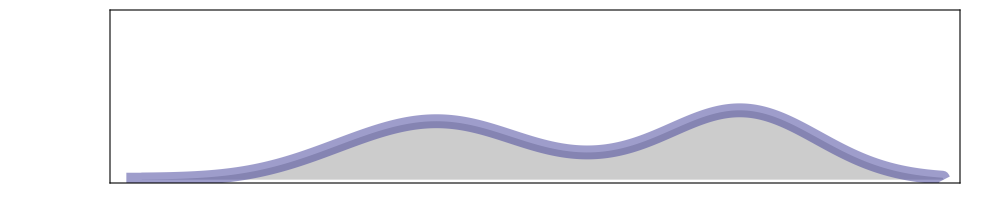
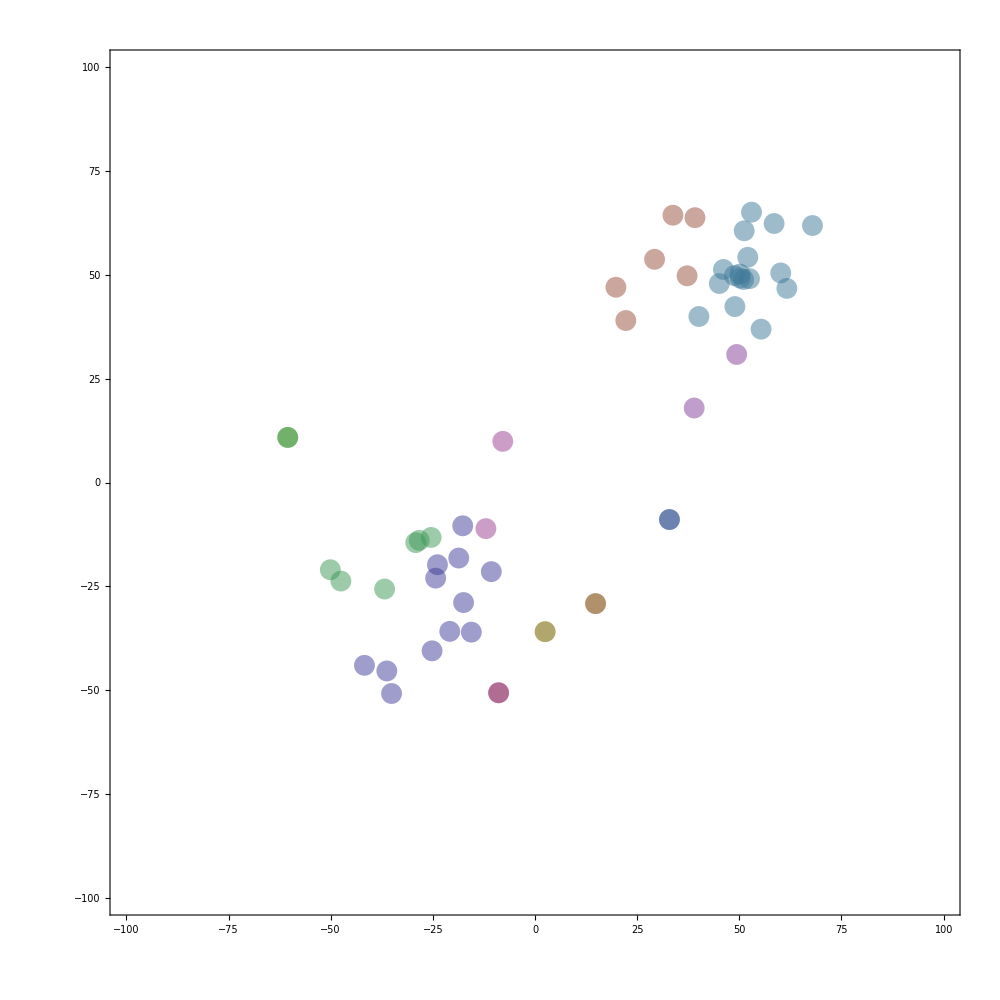
| -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
{imageSize,imagePadding,plotRange}={1000,50,{-100,100}};
histograms=SmoothHistogram[#,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange,{0,.025}},
AspectRatio->.2,
Axes->False,
FrameTicks->{None,None},
Filling->Bottom,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]&/@{sampledCoordinates[[All,1]],sampledCoordinates[[All,2]]};
scatter=ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
BaseStyle->25,
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange,plotRange},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.015],Opacity[.5]}],
ImageSize->imageSize,
ImagePadding->imagePadding
];
Grid[{
{"",Rotate[histograms[[1]]//Show[#,ImagePadding->{{imagePadding,imagePadding},{0,0}}]&,0Degree],""},
{Rotate[histograms[[2]]//Show[#,ImagePadding->{{imagePadding,imagePadding},{0,0}}]&,90Degree],scatter//Show[#,ImagePadding->{{imagePadding,imagePadding},{imagePadding,imagePadding}}]&,""}
}]
```

#### Iterated Complex

```mathematica
{repetitions,scenarioName,midID}={100,"TwoTowns","DARPA"};
{centroids,pointsNumber,clusteringMethod}={{{-25,-25},{50,50}},20,"NeighborhoodContraction"};
{imageSize,imagePadding,plotRange}={500,50,{{-100,100},{0,0.025}}};
(*Export Cycle*)
pointsTriplets=Table[
(*Sample Points and Find Clusters*)
points=Join[{
DistributionIntoKernel[WeibullDistribution[2,25],centroids[[1]],pointsNumber],
DistributionIntoKernel[NormalDistribution[0,20],centroids[[2]],pointsNumber]
}];
sampledCoordinates=Flatten[points,1];
clusteredCoordinates=FindClusters[sampledCoordinates,Method->clusteringMethod];
eucledianDistances=CalculateEuclideanDistances[sampledCoordinates];
clustersPosition=Position[clusteredCoordinates,#][[1,1]]&/@sampledCoordinates;
(*Generate Plots*)
histograms=SmoothHistogramPlot[#,{imageSize,imagePadding},plotRange]&/@Transpose[sampledCoordinates];
scatter=ListPlotScatter[clusteredCoordinates,{imageSize,imagePadding},plotRange];
grid=Grid[{
{"",Rotate[histograms[[1]]//Show[#,ImagePadding->{{imagePadding,imagePadding},{0,0}}]&,0Degree],""},
{Rotate[histograms[[2]]//Show[#,ImagePadding->{{imagePadding,imagePadding},{0,0}}]&,90Degree],scatter//Show[#,ImagePadding->{{imagePadding,imagePadding},{imagePadding,imagePadding}}]&,""}
}];
grid=Grid[{{grid,MatrixPlot[eucledianDistances,ColorFunction->"LakeColors",ImageSize->imageSize]}}];
folderPath="./PaperScenarios/Distributions_"<>scenarioName<>"/"<>StringPadLeft[midID,6,"0"];
CreateDirectory[folderPath]//Quiet;
CreateDirectory[folderPath<>"/"<>"images"]//Quiet;
(*Export[folderPath<>"/"<>scenarioName<>"_Mov_"<>StringPadLeft[ToString[repetition],6,"0"]<>".csv",transitionsMatrix];*)
Export[folderPath<>"/"<>scenarioName<>"_Crd_"<>StringPadLeft[ToString[repetition],6,"0"]<>".csv",Flatten/@({sampledCoordinates,clustersPosition}//Transpose)];
(*Export[folderPath<>"/"<>scenarioName<>"_Cls_"<>StringPadLeft[ToString[repetition],6,"0"]<>".csv",clusteredCoordinates];*)
Export[folderPath<>"/images/"<>scenarioName<>StringPadLeft[ToString[repetition],6,"0"]<>".png",grid,ImageSize->imageSize*5];
,{repetition,repetitions}];
```

### Bands

```mathematica
(*datapairs=Join[
GaussianRandomData[100,{-2,1},.3],
GaussianRandomData[100,{1,-1.8},.2],
GaussianRandomData[100,{-1,-1.1},.4],
GaussianRandomData[100,{1.75,1.75},0.1]
];
cl=FindClusters[datapairs];
ListPlot[cl,PlotTheme->"RandomPointsPlot"]*)
```

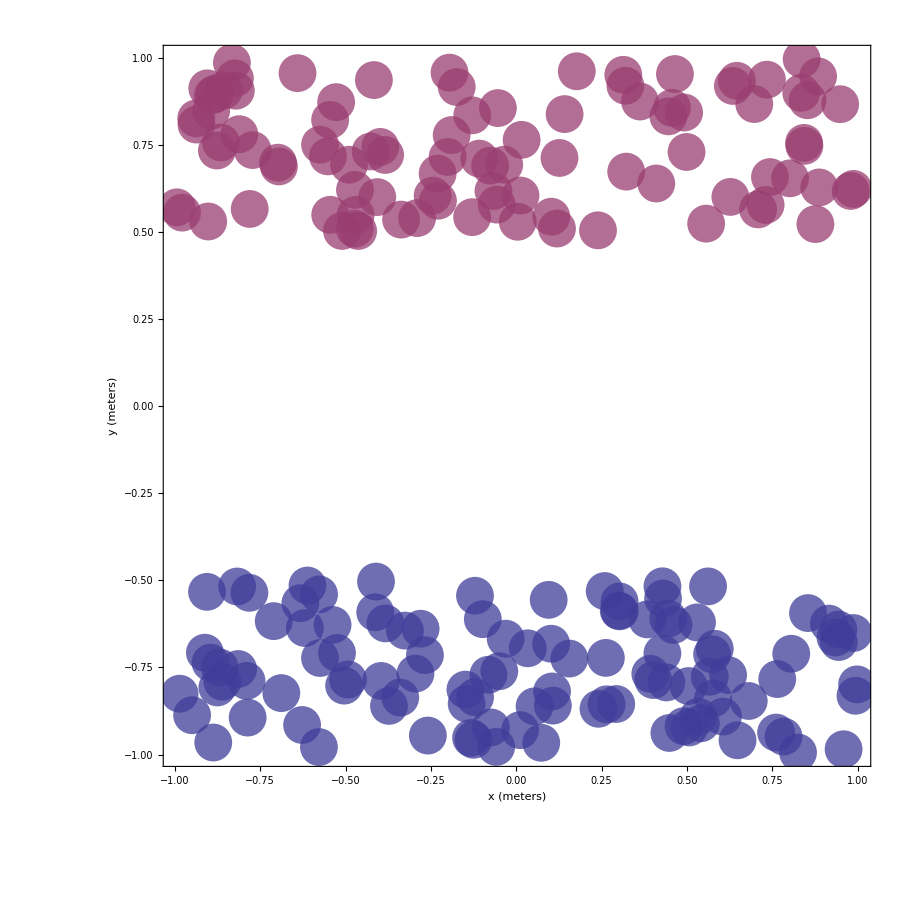

```mathematica
Dis=MixtureDistribution[{1,1},{
UniformDistribution[{{-1,1}, {-1,-.5}}],
UniformDistribution[{{-1,1},{.5,1}}]
}];
stripes=RandomVariate[Dis,200];
ListPlot[FindClusters[stripes],
PlotTheme->"RandomPointsPlot"
]
```

```mathematica
datapairs=
Join[
LevyRandomData[50,{-10,10},.3],
LevyRandomData[50,{10,-10},.2]
];
cl=FindClusters[datapairs];
ListPlot[cl,
PlotTheme->"RandomPointsPlot"
]
```

FindClusters::mlbddata: The data is not formatted correctly.

ListPlot::lpn: FindClusters[LevyRandomData[50.,{-10.,10.},0.3,50.,{10.,-10.},0.2]] is not a list of numbers or pairs of numbers.

FindClusters::mlbddata: The data is not formatted correctly.

General::stop: Further output of FindClusters::mlbddata will be suppressed during this calculation.

ListPlot::lpn: FindClusters[LevyRandomData[50.,{-10.,10.},0.3,50.,{10.,-10.},0.2]] is not a list of numbers or pairs of numbers.

ListPlot[FindClusters[LevyRandomData[50,{-10,10},0.3,50,{10,-10},0.2]],PlotTheme→RandomPointsPlot]

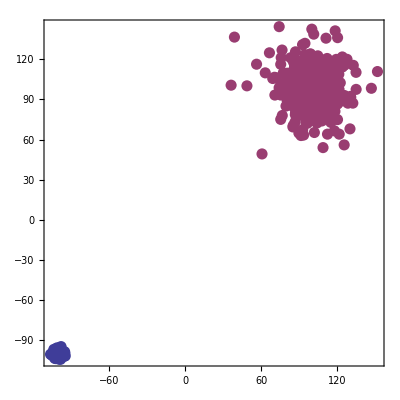

```mathematica
points=Join[{
DistributionIntoKernel[LaplaceDistribution[0,1],{-100,-100},1000],
DistributionIntoKernel[LaplaceDistribution[0,10],{100,100},1000]
}];
ListPlot[points,PlotTheme->"RandomPointsPlot"]
```

## Legacy

```mathematica
map=ListPlot[
cityCoordinates,
PlotStyle->Directive[White,Opacity[.9],PointSize[.02]],
Prolog->{EdgeForm[Directive[Thickness[.0025],White]],Darker[White,1],countryMap},
AspectRatio->1,
Axes->False,
ImageSize->1000,
Frame->True,
FrameStyle->Directive[{White,Thickness[.01]}],
FrameTicksStyle->.01,
Background->Lighter[Black,.1]
];
transitions=Grid[{
{MatrixPlot[distances,ColorFunction->"LakeColors",ImageSize->510,FrameTicksStyle->.001,Frame->None]},
{MatrixPlot[migrationProbabilities,ColorFunction->"LakeColors",ImageSize->510,FrameTicksStyle->.001,Frame->None]}
}];
Grid[{{map,transitions}}];
```

# Paper Scenarios

## Point

```mathematica
scenarioName="Point";
transitionsMatrix={1};
coords={0,0};
Export["./PaperScenarios/01"<>scenarioName<>"/"<>scenarioName<>"_Matrix.csv",transitionsMatrix]
Export["./PaperScenarios/01"<>scenarioName<>"/"<>scenarioName<>"_Coordinates.csv",coords]
```

Export::nodir: Directory /Users/sanchez.hmsc/PaperScenarios/01Point/ does not exist.

OpenWrite::noopen: Cannot open /Users/sanchez.hmsc/PaperScenarios/01Point/Point_Matrix.csv.

$Failed

Export::nodir: Directory /Users/sanchez.hmsc/PaperScenarios/01Point/ does not exist.

OpenWrite::noopen: Cannot open /Users/sanchez.hmsc/PaperScenarios/01Point/Point_Coordinates.csv.

$Failed

## Line

```mathematica
nonMigratoryForce=100;
scenarioName="Line";
{samples,center,σ,repetitions}={50,0,1,50};
distribution=NormalDistribution[0,σ];
```

```mathematica
Table[
sampledPositions=RandomReal[distribution,samples]+center;
sampledCoordinates={#,0}&/@sampledPositions;
clusteredCoordinates=FindClusters[sampledCoordinates, Method->"DBSCAN"];
grid=Grid[{{
ListPlot[clusteredCoordinates,
PlotRange->{{-3σ,3σ},{-1,1}},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Opacity[.5]}],
ImageSize->500
],
SmoothHistogram[sampledPositions,
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->500,
PlotRange->{{-3σ,3σ},Automatic}
]
}}];
folderPath="./PaperScenarios/02"<>scenarioName<>"/"<>StringPadLeft[ToString[σ*100],6,"0"];
CreateDirectory[folderPath]//Quiet;
CreateDirectory[folderPath<>"/"<>"images"]//Quiet;
Export[folderPath<>"/"<>scenarioName<>"_Mov_"<>StringPadLeft[ToString[repetition],6,"0"]<>".csv",transitionsMatrix];
Export[folderPath<>"/"<>scenarioName<>"_Crd_"<>StringPadLeft[ToString[repetition],6,"0"]<>".csv",coords];
Export[folderPath<>"/"<>scenarioName<>"_Cls_"<>StringPadLeft[ToString[repetition],6,"0"]<>".csv",clusteredCoordinates];
Export[folderPath<>"/images/"<>scenarioName<>StringPadLeft[ToString[repetition],6,"0"]<>".png",grid]
,{repetition,1,repetitions}]
```

{./PaperScenarios/02Line/000100/images/Line000001.png,./PaperScenarios/02Line/000100/images/Line000002.png,./PaperScenarios/02Line/000100/images/Line000003.png,./PaperScenarios/02Line/000100/images/Line000004.png,./PaperScenarios/02Line/000100/images/Line000005.png,./PaperScenarios/02Line/000100/images/Line000006.png,./PaperScenarios/02Line/000100/images/Line000007.png,./PaperScenarios/02Line/000100/images/Line000008.png,./PaperScenarios/02Line/000100/images/Line000009.png,./PaperScenarios/02Line/000100/images/Line000010.png,./PaperScenarios/02Line/000100/images/Line000011.png,./PaperScenarios/02Line/000100/images/Line000012.png,./PaperScenarios/02Line/000100/images/Line000013.png,./PaperScenarios/02Line/000100/images/Line000014.png,./PaperScenarios/02Line/000100/images/Line000015.png,./PaperScenarios/02Line/000100/images/Line000016.png,./PaperScenarios/02Line/000100/images/Line000017.png,./PaperScenarios/02Line/000100/images/Line000018.png,./PaperScenarios/02Line/000100/images/Line000019.png,./PaperScenarios/02Line/000100/images/Line000020.png,./PaperScenarios/02Line/000100/images/Line000021.png,./PaperScenarios/02Line/000100/images/Line000022.png,./PaperScenarios/02Line/000100/images/Line000023.png,./PaperScenarios/02Line/000100/images/Line000024.png,./PaperScenarios/02Line/000100/images/Line000025.png,./PaperScenarios/02Line/000100/images/Line000026.png,./PaperScenarios/02Line/000100/images/Line000027.png,./PaperScenarios/02Line/000100/images/Line000028.png,./PaperScenarios/02Line/000100/images/Line000029.png,./PaperScenarios/02Line/000100/images/Line000030.png,./PaperScenarios/02Line/000100/images/Line000031.png,./PaperScenarios/02Line/000100/images/Line000032.png,./PaperScenarios/02Line/000100/images/Line000033.png,./PaperScenarios/02Line/000100/images/Line000034.png,./PaperScenarios/02Line/000100/images/Line000035.png,./PaperScenarios/02Line/000100/images/Line000036.png,./PaperScenarios/02Line/000100/images/Line000037.png,./PaperScenarios/02Line/000100/images/Line000038.png,./PaperScenarios/02Line/000100/images/Line000039.png,./PaperScenarios/02Line/000100/images/Line000040.png,./PaperScenarios/02Line/000100/images/Line000041.png,./PaperScenarios/02Line/000100/images/Line000042.png,./PaperScenarios/02Line/000100/images/Line000043.png,./PaperScenarios/02Line/000100/images/Line000044.png,./PaperScenarios/02Line/000100/images/Line000045.png,./PaperScenarios/02Line/000100/images/Line000046.png,./PaperScenarios/02Line/000100/images/Line000047.png,./PaperScenarios/02Line/000100/images/Line000048.png,./PaperScenarios/02Line/000100/images/Line000049.png,./PaperScenarios/02Line/000100/images/Line000050.png}

## Radial

```mathematica
nonMigratoryForce=100;
scenarioName="Radial";
{samples,center,σ,repetitions}={50,0,10,50};
```

```mathematica
Table[
distribution=DistributionIntoKernel[NormalDistribution[0,σ],{0,0},samples];
sampledCoordinates=distribution;
clusteredCoordinates=FindClusters[sampledCoordinates, Method->"DBSCAN"];
grid=Grid[{{
ListPlot[clusteredCoordinates,
PlotRange->{{-3σ,3σ},{-3σ,3σ}},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Opacity[.5]}],
ImageSize->500
],
SmoothHistogram[{sampledCoordinates[[All,1]],sampledCoordinates[[All,2]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->500,
PlotRange->{{-3σ,3σ},Automatic}
]
}}];
folderPath="./PaperScenarios/03"<>scenarioName<>"/"<>StringPadLeft[ToString[σ*100],6,"0"];
CreateDirectory[folderPath]//Quiet;
CreateDirectory[folderPath<>"/"<>"images"]//Quiet;
Export[folderPath<>"/"<>scenarioName<>"_Mov_"<>StringPadLeft[ToString[repetition],6,"0"]<>".csv",transitionsMatrix];
Export[folderPath<>"/"<>scenarioName<>"_Crd_"<>StringPadLeft[ToString[repetition],6,"0"]<>".csv",coords];
Export[folderPath<>"/"<>scenarioName<>"_Cls_"<>StringPadLeft[ToString[repetition],6,"0"]<>".csv",clusteredCoordinates];
Export[folderPath<>"/images/"<>scenarioName<>StringPadLeft[ToString[repetition],6,"0"]<>".png",grid]
,{repetition,1,repetitions}]
```

{./PaperScenarios/03Radial/001000/images/Radial000001.png,./PaperScenarios/03Radial/001000/images/Radial000002.png,./PaperScenarios/03Radial/001000/images/Radial000003.png,./PaperScenarios/03Radial/001000/images/Radial000004.png,./PaperScenarios/03Radial/001000/images/Radial000005.png,./PaperScenarios/03Radial/001000/images/Radial000006.png,./PaperScenarios/03Radial/001000/images/Radial000007.png,./PaperScenarios/03Radial/001000/images/Radial000008.png,./PaperScenarios/03Radial/001000/images/Radial000009.png,./PaperScenarios/03Radial/001000/images/Radial000010.png,./PaperScenarios/03Radial/001000/images/Radial000011.png,./PaperScenarios/03Radial/001000/images/Radial000012.png,./PaperScenarios/03Radial/001000/images/Radial000013.png,./PaperScenarios/03Radial/001000/images/Radial000014.png,./PaperScenarios/03Radial/001000/images/Radial000015.png,./PaperScenarios/03Radial/001000/images/Radial000016.png,./PaperScenarios/03Radial/001000/images/Radial000017.png,./PaperScenarios/03Radial/001000/images/Radial000018.png,./PaperScenarios/03Radial/001000/images/Radial000019.png,./PaperScenarios/03Radial/001000/images/Radial000020.png,./PaperScenarios/03Radial/001000/images/Radial000021.png,./PaperScenarios/03Radial/001000/images/Radial000022.png,./PaperScenarios/03Radial/001000/images/Radial000023.png,./PaperScenarios/03Radial/001000/images/Radial000024.png,./PaperScenarios/03Radial/001000/images/Radial000025.png,./PaperScenarios/03Radial/001000/images/Radial000026.png,./PaperScenarios/03Radial/001000/images/Radial000027.png,./PaperScenarios/03Radial/001000/images/Radial000028.png,./PaperScenarios/03Radial/001000/images/Radial000029.png,./PaperScenarios/03Radial/001000/images/Radial000030.png,./PaperScenarios/03Radial/001000/images/Radial000031.png,./PaperScenarios/03Radial/001000/images/Radial000032.png,./PaperScenarios/03Radial/001000/images/Radial000033.png,./PaperScenarios/03Radial/001000/images/Radial000034.png,./PaperScenarios/03Radial/001000/images/Radial000035.png,./PaperScenarios/03Radial/001000/images/Radial000036.png,./PaperScenarios/03Radial/001000/images/Radial000037.png,./PaperScenarios/03Radial/001000/images/Radial000038.png,./PaperScenarios/03Radial/001000/images/Radial000039.png,./PaperScenarios/03Radial/001000/images/Radial000040.png,./PaperScenarios/03Radial/001000/images/Radial000041.png,./PaperScenarios/03Radial/001000/images/Radial000042.png,./PaperScenarios/03Radial/001000/images/Radial000043.png,./PaperScenarios/03Radial/001000/images/Radial000044.png,./PaperScenarios/03Radial/001000/images/Radial000045.png,./PaperScenarios/03Radial/001000/images/Radial000046.png,./PaperScenarios/03Radial/001000/images/Radial000047.png,./PaperScenarios/03Radial/001000/images/Radial000048.png,./PaperScenarios/03Radial/001000/images/Radial000049.png,./PaperScenarios/03Radial/001000/images/Radial000050.png}

## Collage

```mathematica
names=FileNames["*.png",Directory[]<>"/PaperScenarios/Distributions_TwoTowns/0DARPA/images/"];
images=Import[#]&/@names;
partitions=Partition[images[[1;;30]],5];
```

```mathematica
Export["grid.png",partitions,ImageSize->2000]
```

grid.png

## Map Coordinates File

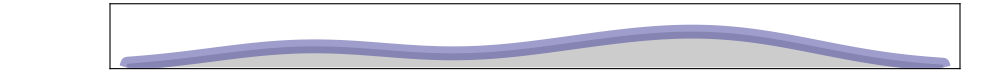
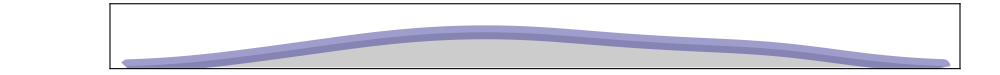
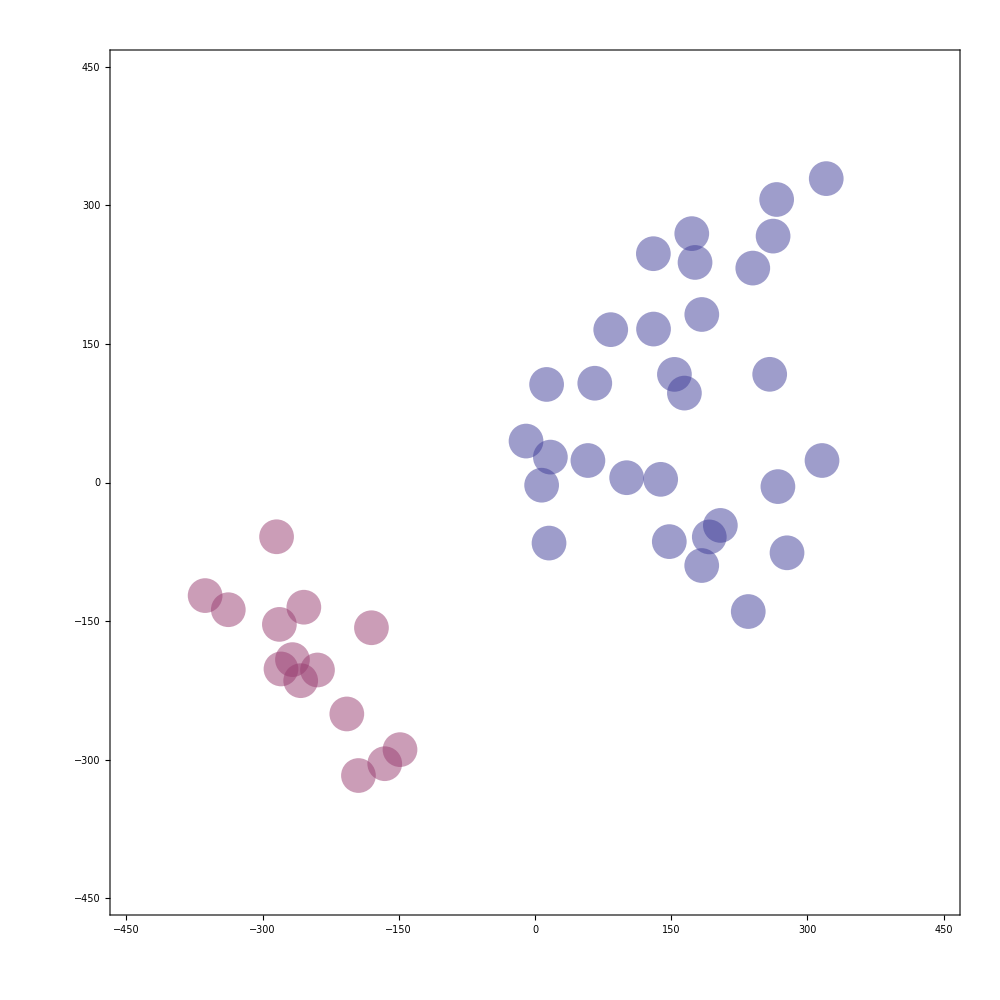
| -Graphics- | 
-Graphics- | -Graphics- |

landscape.png

```mathematica
coords=Import["./DARPADemo/accumulateCityDARPA.csv"][[All,{3,2}]];
{repetitions,scenarioName,midID}={100,"TwoTowns","DARPA"};
{centroids,pointsNumber,clusteringMethod}={{{-700,-25},{50,50}},20,"DBSCAN"};
{imageSize,imagePadding,plotRange}={1000,50,{{-450,450},{0,0.0035}}};
(**)
sampledCoordinates={Transpose[coords][[1]]+00,Transpose[coords][[2]]+50}//Transpose;
clusteredCoordinates=FindClusters[sampledCoordinates,2,Method->"KMeans"];
(**)
range=Range[sampledCoordinates//Length];
clusteredLengths=Length/@clusteredCoordinates;
clusteredIDs=Table[
taken=Take[range,clusteredLengths[[i]]];
range=Drop[range,clusteredLengths[[i]]];
#[[1]]&/@Transpose[{clusteredCoordinates[[i]],taken}]
,{i,1,(clusteredLengths//Length)}];
(**)
eucledianDistances=CalculateEuclideanDistances[sampledCoordinates];
clustersPosition=Position[clusteredCoordinates,#][[1,1]]&/@sampledCoordinates;
(*Generate Plots*)
histograms=SmoothHistogramPlot[#,{imageSize,imagePadding},plotRange]&/@Transpose[sampledCoordinates];
scatter=ListPlotScatter[clusteredIDs,{imageSize,imagePadding},plotRange];
grid=Grid[{
{"",Rotate[histograms[[1]]//Show[#,ImagePadding->{{imagePadding,imagePadding},{0,0}}]&,0Degree],""},
{Rotate[histograms[[2]]//Show[#,ImagePadding->{{imagePadding,imagePadding},{0,0}}]&,90Degree],scatter//Show[#,ImagePadding->{{imagePadding,imagePadding},{imagePadding,imagePadding}}]&,""}
}]
Export["landscape.png",%,ImageSize->2500,ImageResolution->500]
```

```mathematica
(*Distances*)
distances=eucledianDistances;
MatrixPlot[distances,ColorFunction->"LakeColors",Mesh->All,MeshStyle->Opacity[.1],PlotLegends->Automatic,ImageSize->Large];
Export["distancesMatrix.png",%,ImageSize->2500,ImageResolution->500];
(*Transitions*)
transitions=Import["./DARPADemo/accumulateCityDARPA_exponentialKernel.csv"][[2;;All]];
MatrixPlot[transitions,ColorFunction->"LakeColors",Mesh->All,MeshStyle->Opacity[.1],PlotLegends->Automatic,ImageSize->Large,FrameTicksStyle->20];
Export["transitionsMatrix.png",%,ImageSize->2500,ImageResolution->500];
```

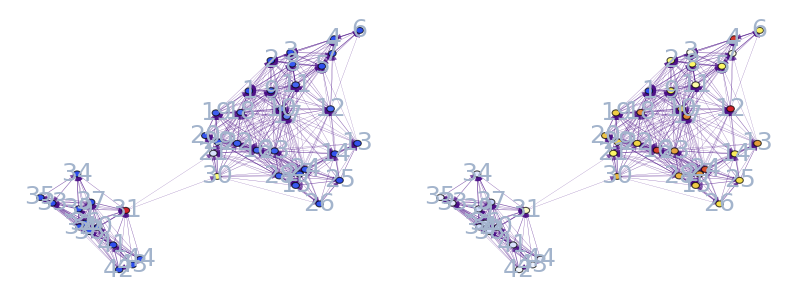

```mathematica
styles={
ConstantArray[{Directive[Lighter[Pink,0.65],EdgeForm[Directive[Thickness[.0025],Black]]]},30],
ConstantArray[{Directive[Lighter[Blue,.9],EdgeForm[Directive[Thickness[.0025],Black]]]},44-30]
}//Flatten[#]&;
ids=ToString/@Range[styles//Length];
stylesList=(#[[2]]->#[[1]])&/@({styles,ids}//Transpose);
(**)
graph=GraphTransitionsFrequenciesWithMax[
{
Chop[Quiet[1/distances]//LowerTriangularize//ReplacePart[#,{i_,i_}->0]&,.004],
ToString/@Range[Length[coords]]
},.0001,
VertexCoordinates->coords,
LineThickness->.0000025,
ImageSize->2000,
VertexStyle->stylesList,
VertexLabelStyle->Directive[25],
VariableStyle->"Both",
VertexSize->1
];
graph2=GraphTransitionsFrequenciesWithMax[
{
Chop[Quiet[1/distances]//LowerTriangularize//ReplacePart[#,{i_,i_}->0]&,.004],
ToString/@Range[Length[coords]]
},.0001,
VertexCoordinates->coords,
LineThickness->.0000025,
ImageSize->2000,
VertexStyle->stylesList,
VertexLabelStyle->Directive[25],
VariableStyle->"Both",
VertexSize->1
];
cc=BetweennessCentrality[graph2];
cc1g=HighlightGraph[graph,Table[Style[VertexList[graph]⟦i⟧,ColorData["TemperatureMap"][cc⟦i⟧/Max[cc]]],{i,VertexCount[graph]}],ImageSize->1500];
(*Export["centralityBetweenNetwork.png",%,ImageSize->2500,ImageResolution->500];*)
cc=ClosenessCentrality[graph2];
cc2g=HighlightGraph[graph,Table[Style[VertexList[graph]⟦i⟧,ColorData["TemperatureMap"][cc⟦i⟧/Max[cc]]],{i,VertexCount[graph]}],ImageSize->1500];
(*Export["centralityClosenessNetwork.png",%,ImageSize->2500,ImageResolution->500];*)
Grid[{{cc1g,cc2g}}]
(*FindGraphCommunities[graph,Method->"Centrality"]
HighlightGraph[graph,Map[Subgraph[graph,#]&, %]]*)
```

## Drafts and Demos

```mathematica
network=GraphTransitionsFrequencies[{distances,ToString/@Range[distances//Length]}];
Mean[Mean/@GraphDistanceMatrix[network]]
LocalClusteringCoefficient[network]
```

327.187

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

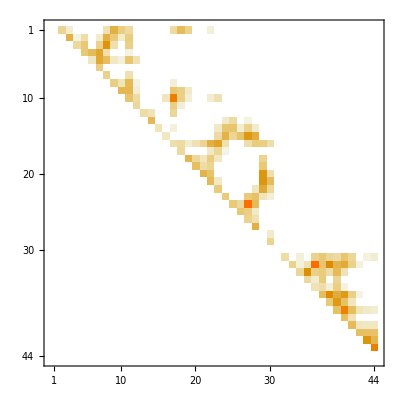

```mathematica
Chop[transitions//UpperTriangularize//ReplacePart[#,{i_,i_}->0]&,10^-6]//MatrixPlot
```

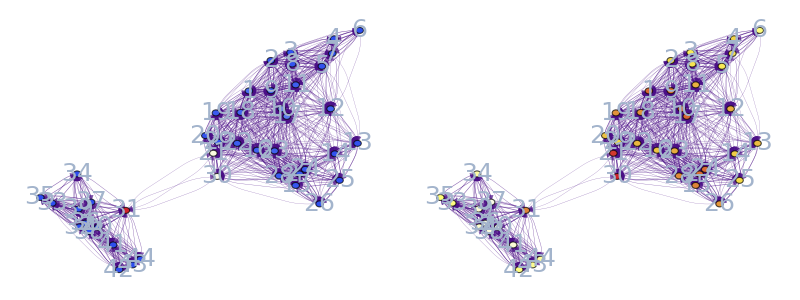

```mathematica
graph=GraphTransitionsFrequenciesWithMax[
{
Chop[Quiet[1/distances]//ReplacePart[#,{i_,i_}->0]&,.004],
ToString/@Range[Length[coords]]
},.0001,
VertexCoordinates->coords,
LineThickness->.0000025,
ImageSize->2000,
VertexStyle->stylesList,
VertexLabelStyle->Directive[25],
VariableStyle->"Both",
VertexSize->1
];
cc=BetweennessCentrality[graph];
cc1g=HighlightGraph[graph,Table[Style[VertexList[graph]⟦i⟧,ColorData["TemperatureMap"][cc⟦i⟧/Max[cc]]],{i,VertexCount[graph]}],ImageSize->1500];
cc=ClosenessCentrality[graph];
cc2g=HighlightGraph[graph,Table[Style[VertexList[graph]⟦i⟧,ColorData["TemperatureMap"][cc⟦i⟧/Max[cc]]],{i,VertexCount[graph]}],ImageSize->1500];
Grid[{{cc1g,cc2g}}]
```

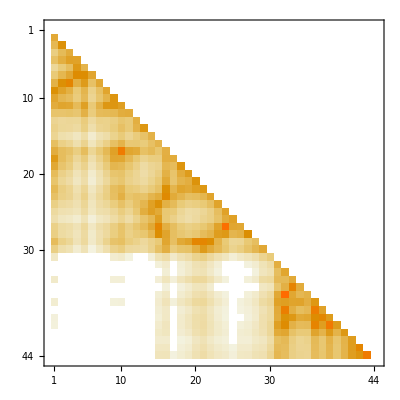

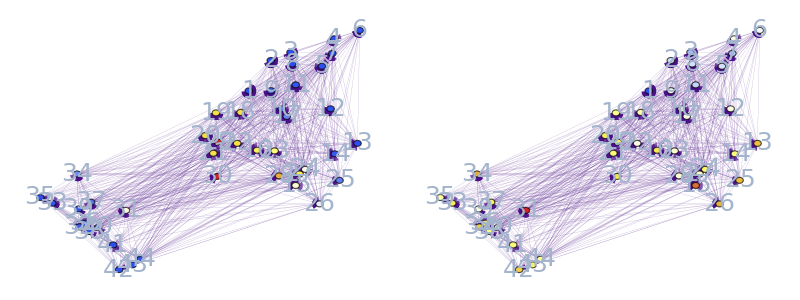

```mathematica
transMatrix=Chop[Quiet[1/distances]//LowerTriangularize//ReplacePart[#,{i_,i_}->0]&,.002];
transMatrix//MatrixPlot
graph=GraphTransitionsFrequenciesWithMax[{transMatrix,ToString/@Range[distances//Length]},.001,
VertexCoordinates->coords,
LineThickness->.0000025,
ImageSize->2000,
VertexStyle->stylesList,
VertexLabelStyle->Directive[25],
VariableStyle->"Both",
VertexSize->1 ];
cc=BetweennessCentrality[graph];
cc1g=HighlightGraph[graph,Table[Style[VertexList[graph]⟦i⟧,ColorData["TemperatureMap"][cc⟦i⟧/Max[cc]]],{i,VertexCount[graph]}],ImageSize->1500];
cc=ClosenessCentrality[graph];
cc2g=HighlightGraph[graph,Table[Style[VertexList[graph]⟦i⟧,ColorData["TemperatureMap"][cc⟦i⟧/Max[cc]]],{i,VertexCount[graph]}],ImageSize->1500];
Grid[{{cc1g,cc2g}}]
```

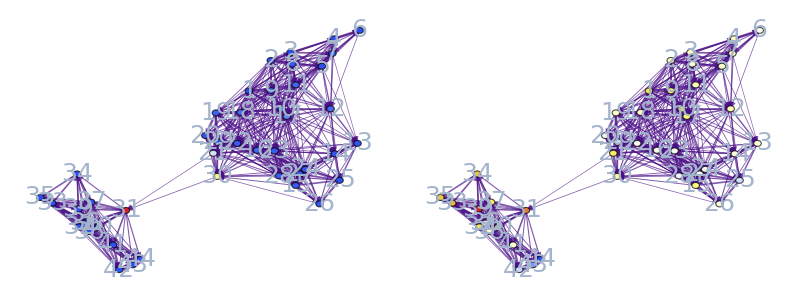

```mathematica
graph=GraphTransitionsFrequenciesWithMax[
{
Chop[Quiet[1/distances]//UpperTriangularize//ReplacePart[#,{i_,i_}->0]&,.004]+Chop[Quiet[1/distances]//UpperTriangularize//ReplacePart[#,{i_,i_}->0]&,.004]*2,
ToString/@Range[Length[coords]]
},.0001,
VertexCoordinates->coords,
LineThickness->.0000025,
ImageSize->2000,
VertexStyle->stylesList,
VertexLabelStyle->Directive[25],
VariableStyle->"Both",
VertexSize->1
];
cc=BetweennessCentrality[graph];
cc1g=HighlightGraph[graph,Table[Style[VertexList[graph]⟦i⟧,ColorData["TemperatureMap"][cc⟦i⟧/Max[cc]]],{i,VertexCount[graph]}],ImageSize->1500];
cc=ClosenessCentrality[graph];
cc2g=HighlightGraph[graph,Table[Style[VertexList[graph]⟦i⟧,ColorData["TemperatureMap"][cc⟦i⟧/Max[cc]]],{i,VertexCount[graph]}],ImageSize->1500];
Grid[{{cc1g,cc2g}}]
```